# Operating with the Fresco files

## Setting current directory, file names etc.

```mathematica
frescoExe=If[$OperatingSystem=="Windows","frescoWin.exe"]
```

frescoWin.exe

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\CAMPIT\Documents\GitHub\menim_jumys_codym

```mathematica
directoryName="2H13C_15MEV\\elastic_inelastic_channels\\";
If[!DirectoryQ[directoryName],CreateDirectory[directoryName]]
```

```mathematica
FileNames["*.txt",directoryName];
currectFile=%
```

{2H13C_15MEV\elastic_inelastic_channels\2H13C.txt}

## Run fresco

```mathematica
plotFromFile[fileName_,expFile_:"_",plotLabel_:""]:=If[FileExistsQ[fileName],
Module[{importedData,plotData,labelPlot,plot,subLabelPlot,exp,expPlot},
importedData=Import[fileName,"Table"];
plotData=Cases[importedData,{_Real,_Real}];
labelPlot=Cases[importedData,{"@subtitle",__}];
labelPlot=Flatten[Drop[labelPlot,None,1]];
subLabelPlot=Flatten[Cases[importedData,{"#legend",__}]];
labelPlot=StringJoin[labelPlot,"\n",subLabelPlot⟦4⟧];
plot=ListLogPlot[plotData,Joined->True,Frame->True,AspectRatio->1.5,FrameLabel->{"θ_cm, degree","dΩ/dσ, mb/sr"},ImageSize->Medium,PlotLabel->plotLabel];
If[expFile≠ "_",expPlot=ListLogPlot[
Cases[
Import[StringJoin[directoryName,expFile],"Table"]
,{_Real,_Real}]
];

exp=Export[StringJoin[directoryName,StringReplace[fileName,"."->""],".pdf"],Show[plot,expPlot,PlotRange->Automatic],"PDF"];
Show[plot,expPlot,PlotRange->Automatic]
,
exp=Export[StringJoin[directoryName,StringReplace[fileName,"."->""],".pdf"],plot,"PDF"];
plot]
]];
```

```mathematica
StringJoin[frescoExe," < ", currectFile, " > ",StringDrop[currectFile,-4],".out" ]
Run[% ]
```

frescoWin.exe < 2H13C_15MEV\elastic_inelastic_channels\2H13C.txt > 2H13C_15MEV\elastic_inelastic_channels\2H13C.out

0

## Plot and Export calculated Data

```mathematica
expFileNameList={"\\exp\\14.dat","\\exp\\36814.dat","\\exp\\7514.dat","\\exp\\68614.dat"};
csFileNameList={"fort.201","fort.202","fort.203","fort.204"};
```

```mathematica
SetAttributes[plotFromFile,Listable];
```

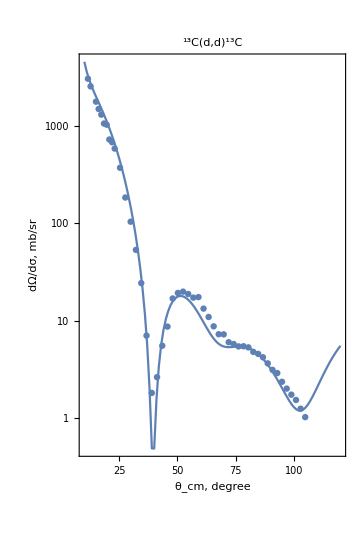

```mathematica
plotFromFile["fort.201","\\exp\\14.dat","^13C(d,d)^13C"]
```

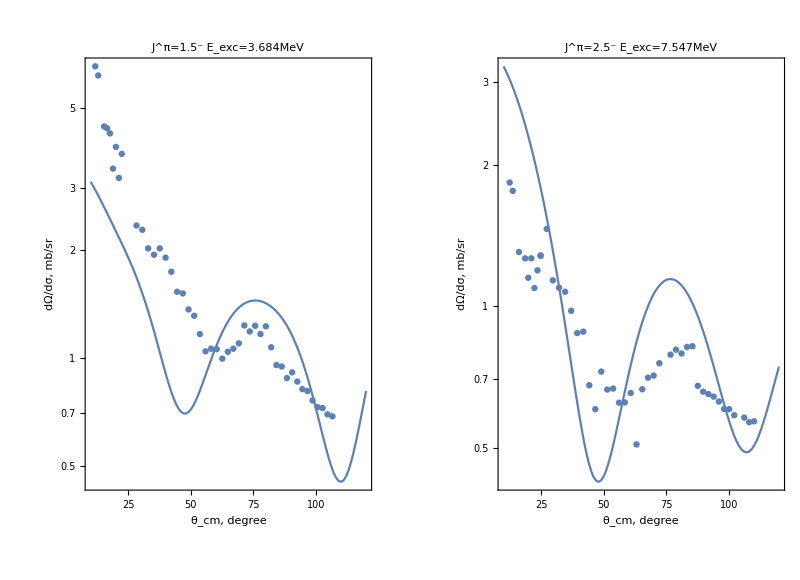

```mathematica
{plotFromFile["fort.202","//exp//36814.dat","C(d,d)^13C^* (1.5^- 3.68)"],plotFromFile["fort.203","//exp//7514.dat","C(d,d)^13C^* (2.5^- 7.54)"]};
GraphicsRow[%]
```

```mathematica
Run["del fort.*"]
```

0